# 2. izpit – Mathematica

## Računalniški praktikum 2024/25

Študijske smeri : Finančna matematika, Matematika, Pedagoška matematika

## Podatki o študentu

Vpišite svoje podatke

Ime:

Priimek:

Vpisna številka:

## Navodila

V tem delu izpita sta dve nalogi, ki sta skupaj vredni 32 točk od 100 možnih na izpitu.
Vsako nalogo rešujte v svojem razdelku.

## 1. naloga [12 točk]

1. (4 točke)  Izračunajte prvi odvod funkcije ln(sin(e^(2x))) in ga poenostavite.
2. (4 točke) Numerično izračunajte ničlo funkcije  (cos(x))/(e^(x^3-1)) z začetnim približkom x = 1 .
3. (4 točke) Na 5 decimalk natančno s pomočjo funkcij FromContinuedFraction in Range izračunajte izraz

1+1/(2+1/(3+1/(⋱_(+1/2025))))

```mathematica
Simplify[D[Log[Sin[E^2x]], x]]
FindRoot[Cos[x]/(E^(x^3 - 1)),{x,1}]
N[FromContinuedFraction[{Range[2025]}], 6]
```

ⅇ^2 Cot[ⅇ^2 x]

{x→1.5708}

1.43313

## 2. naloga [20 točk]

Naj bo dana funkcija f(n)=1/(9 n^2+15 n+4).
1. (5 točk) Definirajte funkcijo f  in izračunajte f(2025).
2. (5 točk) S pomočjo funkcije DiscretePlot narišite točkovni graf f(n) za naravna števila 1≤n≤50.
3. (5 točk) Definirajte funkcijo g kot vsoto g(m) = f(m)+f(m+1)+…+f(2025m).
4. (5 točk) Izračunajte limito lim_(m→∞) g(m).

1/36936004

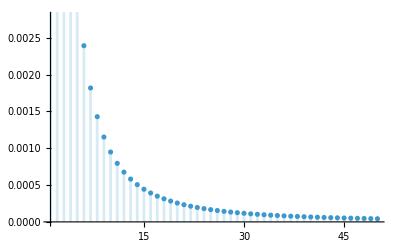

0

```mathematica
f[n_]:= 1/(9n^2+15n+4)
f[2025]
DiscretePlot[f[n], {n, 1, 50}]
g[m_]:= Sum[f[m + k], {k, 0, 2024m}]
Limit[g[m], m ->Infinity]
```